## Standard Ricker model - EWS intervals

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal/models_ricker/ricker_std"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-0.2;
bh=1.2;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="tmax400sims100";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews.csv"];
```

```mathematica
(* Import EWS DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

100

```mathematica
(* Realisation number to display *)
displayNum=4;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

```mathematica
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
```

```mathematica
(* Extract info of one trajectory *)
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
tVals = trajVals[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
```

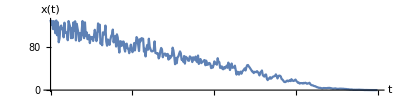

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[trajVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
AxesLabel->{"t","x(t)"},
PlotRange->{{0,tmax},All}]
```

### Plot format adjustment

```mathematica
rTicks=Round[Range[bh,bl,-0.2],0.1];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

```mathematica
rTicks
```

{1.2,1.,0.8,0.6,0.4,0.2,0.,-0.2}

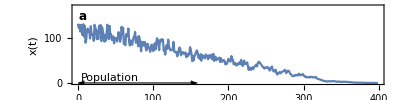

```mathematica
plotTraj=Show[plotX,
PlotRange->{{0,tmax},{0,170}},
ImageSize->imgs,
LabelStyle->ls,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Growth rate, r"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Arrowheads[{-aHeadSize,aHeadSize}*0.7],
Thickness[0.002],
Arrow[{Scaled[{0,0.2},{0,0}],Scaled[{0,0.2},{windowComps*dt2,0}]}]
}
]
```

## EWS Plots

### Variance

```mathematica
(* plot colour *)
colVar=TMBcolours[[2]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
varEws=Table[
DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}],
{realNum,1,numSims}];
```

```mathematica
(* Compute intervals *)
timeVals=varEws[[1,;;,1]];
varEwsMean=Mean[varEws[[;;,;;,2]]];
varEwsSD=StandardDeviation[varEws[[;;,;;,2]]];
```

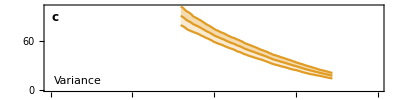

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotVar=ListLinePlot[Transpose[{timeVals,#}]&/@{varEwsMean-varEwsSD,varEwsMean,varEwsMean+varEwsSD},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
(* plot colour *)
colCV=TMBcolours[[3]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
cvEws=Table[
DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}],
{realNum,1,numSims}];
```

```mathematica
(* Compute intervals *)
timeVals=cvEws[[1,;;,1]];
cvEwsMean=Mean[cvEws[[;;,;;,2]]];
cvEwsSD=StandardDeviation[cvEws[[;;,;;,2]]];
```

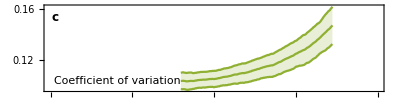

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotCv=ListLinePlot[Transpose[{timeVals,#}]&/@{cvEwsMean-cvEwsSD,cvEwsMean,cvEwsMean+cvEwsSD},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{1->{2},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colCV,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax

```mathematica
(* plot colour *)
colSmax=TMBcolours[[4]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

```mathematica
(* Compute intervals *)
timeVals=smaxEws[[1,;;,1]];
smaxEwsMean=Mean[smaxEws[[;;,;;,2]]];
smaxEwsSD=StandardDeviation[smaxEws[[;;,;;,2]]];
```

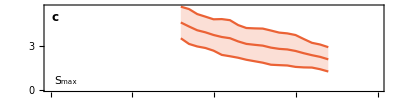

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxMean=ListPlot[Transpose[{timeVals,#}]&/@{smaxEwsMean-smaxEwsSD,smaxEwsMean,smaxEwsMean+smaxEwsSD},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{1->{2},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxMean,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max",ls],textPos,{-1,0}]}]
```

### Smax/Mean

```mathematica
(* plot colour *)
colSmaxMean=TMBcolours[[4]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Mean"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxMeanEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

```mathematica
(* Compute intervals *)
timeVals=smaxMeanEws[[1,;;,1]];
smaxMeanEwsMean=Mean[smaxMeanEws[[;;,;;,2]]];
smaxMeanEwsSD=StandardDeviation[smaxMeanEws[[;;,;;,2]]];
```

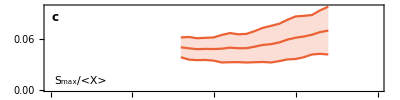

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxMean=ListPlot[Transpose[{timeVals,#}]&/@{smaxMeanEwsMean-smaxMeanEwsSD,smaxMeanEwsMean,smaxMeanEwsMean+smaxMeanEwsSD},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{1->{2},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxMean,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/<X>",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
(* plot colour *)
colSmaxVar=TMBcolours[[5]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxVarEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

```mathematica
(* Compute intervals *)
timeVals=smaxMeanEws[[1,;;,1]];
smaxVarEwsMean=Mean[smaxVarEws[[;;,;;,2]]];
smaxVarEwsSD=StandardDeviation[smaxVarEws[[;;,;;,2]]];
```

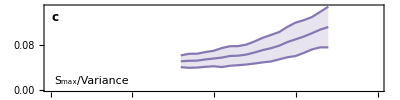

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxVar=ListPlot[Transpose[{timeVals,#}]&/@{smaxVarEwsMean-smaxVarEwsSD,smaxVarEwsMean,smaxVarEwsMean+smaxVarEwsSD},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{1->{2},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/Variance",ls],textPos,{-1,0}]}]
```

### Autocorrelation (combined)

```mathematica
(* plot colour *)
colAC=TMBcolours[[{4,5,7}]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
```

```mathematica
(* Construct relevant sub dataframe *)
acEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws[[i]]}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}],
{realNum,1,numSims},{i,1,3}];
```

```mathematica
acEws//Dimensions
```

{100,3,186,2}

```mathematica
(* line legend *)
legend=LineLegend[colAC,Table["lag-"<>ToString[i],{i,{1,2,3}}],Spacings->{0,0.2},LabelStyle->(ls-1)]
```

```mathematica
(* Compute intervals *)
timeVals=acEws[[1,1,;;,1]];
acEwsMean=Table[Mean[acEws[[;;,lag,;;,2]]],{lag,1,3}];
acEwsSD=Table[StandardDeviation[acEws[[;;,lag,;;,2]]],{lag,1,3}];
```

```mathematica
acEwsSD//Dimensions
```

{3,186}

```mathematica
(* Plot AC EWS for display param *)
ymin=-0.02;
ymax=0.3;
(* Plots for individual lags *)
plotAC1=ListLinePlot[Transpose[{timeVals,#}]&/@{acEwsMean[[1]]-acEwsSD[[1]],acEwsMean[[1]],acEwsMean[[1]]+acEwsSD[[1]]},
PlotStyle->colAC[[1]],
Filling->{1->{2},3->{2}},
PlotLegends->Placed[legend,Scaled[{0.15,0.65}]]];
plotAC2=ListLinePlot[Transpose[{timeVals,#}]&/@{acEwsMean[[2]]-acEwsSD[[2]],acEwsMean[[2]],acEwsMean[[2]]+acEwsSD[[2]]},
PlotStyle->colAC[[2]],
Filling->{1->{2},3->{2}}];
plotAC3=ListLinePlot[Transpose[{timeVals,#}]&/@{acEwsMean[[3]]-acEwsSD[[3]],acEwsMean[[3]],acEwsMean[[3]]+acEwsSD[[3]]},
PlotStyle->colAC[[3]],
Filling->{1->{2},3->{2}}];
```

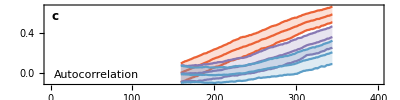

```mathematica
(* Combine plots *)
plotAC=Show[plotAC1,plotAC2,plotAC3,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
PlotRange->{{0,tmax},All},
Axes->False,
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Autocorrelation",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
ktauVar=Table[
KendallTau[DeleteCases[varEws[[realNum]],{_,""}][[;;,1]],DeleteCases[varEws[[realNum]],{_,""}][[;;,2]]],
{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[{ktauVar,ktauVar,ktauVar},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colVar,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of Variation

```mathematica
ktauCv=Table[
KendallTau[DeleteCases[cvEws[[realNum]],{_,""}][[;;,1]],DeleteCases[cvEws[[realNum]],{_,""}][[;;,2]]],
{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[{ktauCv,ktauCv,ktauCv},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colCV,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Mean

```mathematica
ktauSmaxMean=Table[
KendallTau[DeleteCases[smaxMeanEws[[realNum]],{_,""}][[;;,1]],DeleteCases[smaxMeanEws[[realNum]],{_,""}][[;;,2]]],
{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxSmaxMean=BoxWhiskerChart[{ktauSmaxMean,ktauSmaxMean,ktauSmaxMean},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colSmaxMean,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
ktauSmaxVar=Table[
KendallTau[DeleteCases[smaxVarEws[[realNum]],{_,""}][[;;,1]],DeleteCases[smaxVarEws[[realNum]],{_,""}][[;;,2]]],
{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[{ktauSmaxVar,ktauSmaxVar,ktauSmaxVar},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colSmaxVar,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Autocorrelation

```mathematica
acEws//Dimensions
```

{100,3,186,2}

```mathematica
ktauAc=Table[
KendallTau[DeleteCases[acEws[[realNum,lag]],{_,""}][[;;,1]],DeleteCases[acEws[[realNum,lag]],{_,""}][[;;,2]]],
{lag,1,3},{realNum,1,numSims}];
```

```mathematica
(* Box plot *)
boxAc=BoxWhiskerChart[{ktauAc[[1]],ktauAc[[2]],ktauAc[[3]]},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colAC,
ImageSize->imgsBox,
AspectRatio->aRatio*(imgs/imgsBox),
ImagePadding->padBox,
Epilog->{Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}],
Text[Style["h",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
Clear[colFun1]
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
specData//Dimensions
```

{3,81,2}

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[10;;;;4]]
```

{249.,289.,329.}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,_,timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
specData//Dimensions
```

{3,81,2}

```mathematica
(*(* loop power spectrum for display *)
ωVals=pspecs[[1,;;,1]];
ωValsExt={ωVals-2Pi,ωVals,ωVals+2Pi}//Flatten;
pspecsExt=Table[
Transpose[{ωValsExt,Join[pspecs[[i,;;,2]],pspecs[[i,;;,2]],pspecs[[i,;;,2]]]}],
{i,1,Length[pspecs]}];

(* now trim values *)
len=Dimensions[pspecsExt][[2]];
pspecsExt=pspecsExt[[;;,35;;-35]];*)
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
timeRange
```

{249.,329.}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{colFun1[(#-199)/(309-199)]&,timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

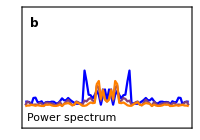

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->{-2,10},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[0,10,2]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAC,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspec,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

```mathematica
plotGrid;
```

```mathematica
Export["figures/intervals_"<>simName<>".png",plotGrid,ImageResolution->100];
```